300

0.62

60

0.13

200

3

30

0.05

1.5

400

0.99

20

1000000

274./(1+k/60)

1/200 (-37538./(1+k/60)^2+82200./(1+k/60))

57.44

1/12 (-81.44+1/200 (-37538./(1+k/60)^2+82200./(1+k/60))-35.62/(1+k/60)-(3.12817 k)/(1+k/60)^2)

125000/3 (-81.44+1/200 (-37538./(1+k/60)^2+82200./(1+k/60))-35.62/(1+k/60)-(3.12817 k)/(1+k/60)^2)^2

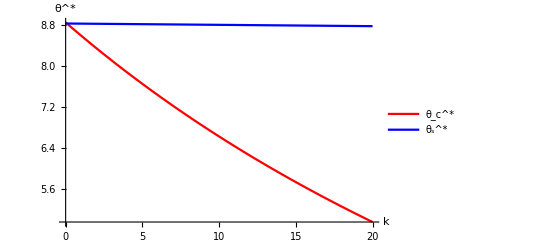

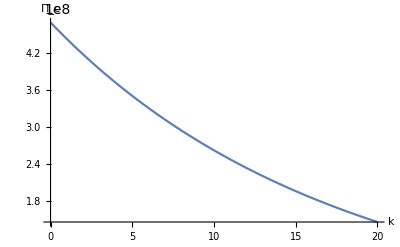

-Graphics-

```mathematica
Set[θ,300]
Set[g,0.62]
Set[v,60]
Set[m,0.13]
Set[b,200]
Set[d,3]
Set[c,30]
Set[μ,0.05]
Set[τ,1.5]
Set[R,400]
Set[r,0.99]
Set[p,20]
Set[n,1000000]
Set[Subscript[e, 1],(θ -b m)/(1+(2k b)/(v R))]
Set[w,1/b(θ Subscript[e, 1]-Subscript[e, 1]^2/2)]
Set[Subscript[U, g],1/b(θ (θ -b g)-(θ -b g)^2/2)-g(θ -b g)-p]
Set[Subscript[A, c],1/(4d)(2d-Subscript[U, g]+w-m Subscript[e, 1]-k/(v R)Subscript[e, 1] Subscript[e, 1]-c)]
Set[Subscript[Π, c],2 n d Subscript[A, c]^2]
Set[Subscript[Π, s],2 n d A ^2-1.29/2 0.2c (τ A n  (2Log[Subscript[e, 2]])/R)^(1/2)];
equs={Subscript[e, 2]==(θ -b y)/(1+(2k b (1-r))/(v R))/.y->m+0.2c 2/(Subscript[e, 2] R)(τ+1.29/2 τ(τ A n  (2Log[Subscript[e, 2]])/R)^(-1/2)),

A==1/(4d)(2d-Subscript[U, g]+u-m Subscript[e, 2]-(k(1-r))/(v R)Subscript[e, 2] Subscript[e, 2]-c-0.2c (2Log[Subscript[e, 2]])/R(τ+1.29/2 τ(τ A n (2Log[Subscript[e, 2]])/R)^(-1/2)))/.u->1/b(θ Subscript[e, 2]-Subscript[e, 2]^2/2)};
rees=Table[{k1,A/.Block[{k=k1},FindRoot[equs,{{A,50},{Subscript[e,2],20}}]]},{k1,0,20,0.5}];
Show[Plot[Subscript[A, c],{k,0,20},AxesLabel->{Style["k",16],Style["θ^*",16]},AxesStyle->Directive[Gray,FontSize->15],PlotStyle->Red,PlotLegends->Placed[{"θ_c^*"},Right]], ListLinePlot[rees,PlotRange->All,AxesLabel->{Style["θ^*",16],"k"},PlotStyle->Blue,PlotLegends->Placed[{"θ_s^*"},Right]] ]
Plot[Subscript[Π, c],{k,0,20},AxesLabel->{"k","Π_c"}]
Plot[Subscript[Π, s],{k,0,20},AxesLabel->{"k","Π_s"}]
```

```mathematica
.
```